## Stock-as-a-Service Analysis

Set the ticker on the line below and re-evaluate the whole notebook...

```mathematica
Ticker="AAPL";
```

```mathematica
TICK = Import[NotebookDirectory[]<>"bytick/scores/basic/"<>Ticker<>".csv"];
```

## Snapshotting

```mathematica
RSD1=DateListPlot[TICK[[All,{1,3}]],PlotLabel->"Relative Strength vs. Dow Jones (RSD)",PlotStyle->{RGBColor[.7,0,0]}];
```

```mathematica
DPC1=DateListPlot[TICK[[All,{1,4}]],PlotLabel->"ΔPrice",PlotStyle->{RGBColor[0,.5,0]}];
```

```mathematica
DVC1=DateListPlot[TICK[[All,{1,5}]],PlotLabel->"ΔVolume",PlotStyle->{RGBColor[0,0,.7]}];
```

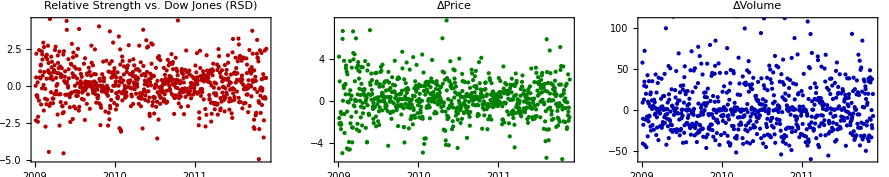

```mathematica
GraphicsRow[{RSD1,DPC1,DVC1}]
```

## Histogramming over 60 days

```mathematica
Manipulate[Histogram[TICK[[date;;date+60,3]],{-10,10,1},PlotRange->{0,35},PlotLabel->"  RSD60"TICK[[date,1]]],{date,1,650,1}]
```

```mathematica
Manipulate[Histogram[TICK[[date;;date+60,4]],{-10,10,1},PlotRange->{0,35},PlotLabel->"  ΔPrice"TICK[[date,1]]],{date,1,650,1}]
```

```mathematica
Manipulate[Histogram[TICK[[date;;date+60,5]],{-100,100,10},PlotRange->{0,20},PlotLabel->"  ΔVol"TICK[[date,1]]],{date,1,650,1}]
```

```mathematica
RSD60=DateListPlot[TICK[[All,{1,7}]],PlotLabel->"Relative Strength vs. Dow Jones (RSD) — 60 Days",PlotStyle->{RGBColor[.7,0,0]},Joined->True];
```

```mathematica
DPC60=DateListPlot[TICK[[All,{1,8}]],PlotLabel->"ΔPrice — 60 Days",PlotStyle->{RGBColor[0,.5,0]},Joined->True];
```

```mathematica
DVC60=DateListPlot[TICK[[All,{1,9}]],PlotLabel->"ΔVolume — 60 Days",PlotStyle->{RGBColor[0,0,.7]}, Joined->True];
```

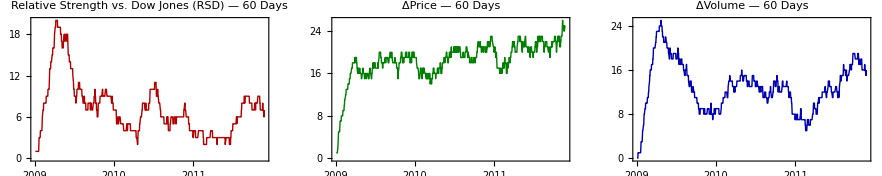

```mathematica
GraphicsRow[{RSD60,DPC60,DVC60}]
```

## Scoring

```mathematica
SnapshottingScore=DateListPlot[TICK[[All,{1,5}]],PlotLabel->"Snapshot Score:\n 3*RSD+2*ΔP+0.1*ΔV",Joined->True];
```

```mathematica
HistogramScore=DateListPlot[TICK[[All,{1,10}]],PlotLabel->"Histogram Score:\n 3*ART(RSD60,1%)+2*ART(ΔP60,2%)+1*ART(ΔV60,10%)",Joined->True];
```

```mathematica
SkylineSnapScore=DateListPlot[Map[{DateList[#[[1]]],#[[2]]}&,Import[NotebookDirectory[]<>"bytick/scores/skyline/snapshot/"<>Ticker<>".csv"][[All,{1,3}]]],
PlotLabel->"Skyline Snapshot Score",Joined->True];
```

```mathematica
SkylineHistoScore=DateListPlot[Map[{DateList[#[[1]]],#[[2]]}&,Import[NotebookDirectory[]<>"bytick/scores/skyline/histogram/"<>Ticker<>".csv"][[All,{1,3}]]],
PlotLabel->"Skyline Histogram Score",Joined->True];
```

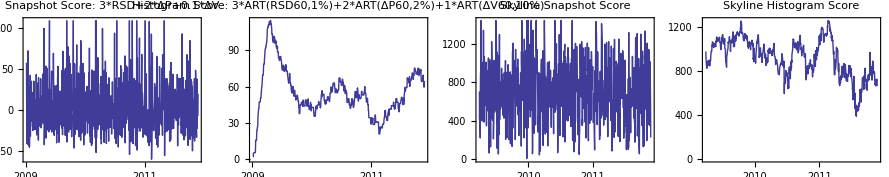

```mathematica
GraphicsRow[{SnapshottingScore,HistogramScore,SkylineSnapScore,SkylineHistoScore}]
```

## Ranking

```mathematica
SnapshottingRank=DateListPlot[{Map[{Partition[#1,3][[1]],500-#1[[-1]]}&,Import[NotebookDirectory[]<>"bytick/ranks/snapshot/"<>Ticker<>".csv"]]}, Joined->True,Filling->Bottom,PlotRange->{Automatic,{0,500}},PlotLabel->"Snapshot Rank",
FrameTicks->{Automatic,Table[{x,500-x},{x,0,500,100}]}];
```

```mathematica
HistogramRank=DateListPlot[{Map[{Partition[#1,3][[1]],500-#1[[-1]]}&,Import[NotebookDirectory[]<>"bytick/ranks/histogram/"<>Ticker<>".csv"]]}, Joined->True,Filling->Bottom,PlotRange->{Automatic,{0,500}},PlotLabel->"Histogram Rank",
FrameTicks->{Automatic,Table[{x,500-x},{x,0,500,100}]}];
```

```mathematica
SkylineSnapRank=DateListPlot[{Map[{Partition[#1,3][[1]],500-#1[[-1]]}&,Import[NotebookDirectory[]<>"bytick/ranks/skyline/snapshot/"<>Ticker<>".csv"]]}, Joined->True,Filling->Bottom,PlotRange->{Automatic,{0,500}},PlotLabel->"Skyline Snapshot Rank",FrameTicks->{Automatic,Table[{x,500-x},{x,0,500,100}]}];
```

```mathematica
SkylineHistoRank=DateListPlot[{Map[{Partition[#1,3][[1]],500-#1[[-1]]}&,Import[NotebookDirectory[]<>"bytick/ranks/skyline/histogram/"<>Ticker<>".csv"]]}, Joined->True,Filling->Bottom,PlotRange->{Automatic,{0,500}},PlotLabel->"Skyline Histogram Rank",FrameTicks->{Automatic,Table[{x,500-x},{x,0,500,100}]}];
```

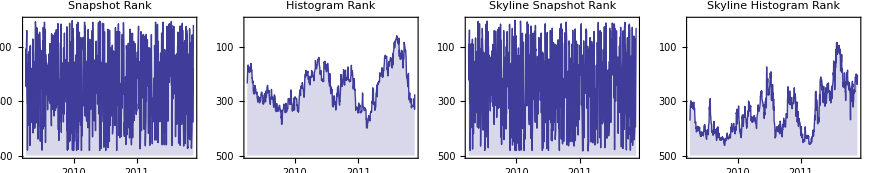

```mathematica
GraphicsRow[{SnapshottingRank,HistogramRank,SkylineSnapRank,SkylineHistoRank}]
```